# Natural gradient optimizer for linear problem

## Create ill-conditioned data

2 dimensions highly correlated with each other, 3rd dimension fully redundant

Loss at w0 1.03475

Grad at w0 {{2.06949,2.05021}}

True cov (1 | 0.99
0.99 | 1)

Data cov (1.03475 | 1.02511
1.02511 | 1.03619)

Data mean {-2.45359×10^-17,1.98286×10^-16}

Augmented loss 1.03475

Augmented grad {{2.06949,2.05021,4.11971}}

~/git/whitening/exp/data/natural_gradient_linear_data.csv

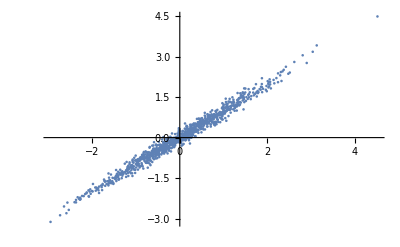

```mathematica
n=2;
e=0.01;
trueCov={{1, 1-e},{1-e,1}};
zero=0&/@Range@n;
normal=MultinormalDistribution[zero,trueCov];
pdf[x_,y_]=PDF[normal,{x,y}];
dsize=1000;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;

(* center the data *)
Xc=Mean@Transpose@X;
X=Transpose[#-Xc&/@Transpose[X]];
wt = {{1,1}}; (* true w *)
w0={{2,1}}; (* initial w *)
Y=Dot[wt, X];
XY = X~Join~Y;
grad[w_]:=2(w.X-Y).Transpose[X]/dsize;
loss[w_]:=Module[{error},
error=(w.X-Y);
First[Flatten[error.errorᵀ/dsize]]
];
Print["Loss at w0 ",loss[w0]];
Print["Grad at w0 ",grad[w0]];
cov=X.Xᵀ/dsize; 

(* sanity checks *)
Print["True cov ",MatrixForm@trueCov];
Print["Data cov ", MatrixForm@cov];
Print["Data mean ", Mean@Transpose@X];

(* Augment with third component being sum of first two *)
Xa= X~Join~{{1,1}.X };
wta=Join[wt,{{0}}, 2];
w0a=Join[w0,{{0}}, 2];
Ya=Dot[wta, Xa];
XYa = Xa~Join~Ya;

cova=Xa.Xaᵀ/dsize; 


grada[wa_]:=2(wa.Xa-Ya).Transpose[Xa]/dsize;
lossa[wa_]:=Module[{error},
error=(wa.Xa-Ya);
First[Flatten[error.errorᵀ/dsize]]
];
Print["Augmented loss ",lossa[w0a]]
Print["Augmented grad ",grada[w0a]]

Export["~/git/whitening/exp/data/natural_gradient_linear_data.csv",XYa]

ListPlot@Transpose@X
```

## Run natural gradient

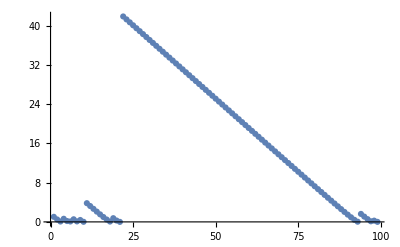

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNatural[loss_,grad_,w0_,lr_]:=Module[{gradstep,err,weightedCov,pre},
{pointList, gradList,preList, lossList}={{},{},{},{}};
err[w_]:=Y-w.Xa;
(* covariance matrix weighted by error *)
weightedCov[w_]:=(
temp=Xa.DiagonalMatrix@Flatten@err[w];
temp.tempᵀ/dsize
);
pre[w_]:=PseudoInverse@weightedCov@w;
w=w0;
For[step=1,step<100,step++,
pointList=pointList~Append~w;
gradList=gradList~Append~grad[w];
preList=preList~Append~pre[w];
lossList=lossList~Append~loss[w];
w=w-lr*grad[w].pre[w];
];
];
optimizeNatural[lossa,grada,w0a,0.5];
Export["~/git/whitening/exp/data/natural_gradient_linear_losses.csv",lossList];
ListPlot@lossList
```

```mathematica
lossList[[;;10]]
```

{1.03475,0.501415,0.077998,0.636779,0.1772,0.0862901,0.533846,0.101634,0.390478,0.0205806}